PROGETTO TD RISAFI NATALE FRANCESCO PIO 223491

```mathematica
(* Dato il sistema dinamico a tempo invariante, tempo discreto (LTI-TD) R^(4x4) costituito dai seguenti parametri: *)
```

```mathematica
A=({{-97/120, 53/120, -1/40, 7/120}, {-1/2, 1/2, 1/2, -1/2}, {-1/2, -1/2, -1/2, -1/2}, {217/120, -53/120, 41/40, -127/120}})
```

{{-97/120,53/120,-1/40,7/120},{-1/2,1/2,1/2,-1/2},{-1/2,-1/2,-1/2,-1/2},{217/120,-53/120,41/40,-127/120}}

```mathematica
B = ({{1/2}, {0}, {0}, {-1/2}})
Cc = ({{0, -2, -4, 0}})
Dd = 0
```

{{1/2},{0},{0},{-1/2}}

{{0,-2,-4,0}}

0

```mathematica
(* Calcolo i modi naturali del sistema; inizio studiando il polinomio caratteristico della matrice A, ed il calcolo dei suoi autovalori: *)
```

```mathematica
poli = Factor[CharacteristicPolynomial[A,λ ]]
```

1/60 (1+2 λ)^2 (2+3 λ) (1+5 λ)

```mathematica
Eigenvalues[A]
```

{-2/3,-1/2,-1/2,-1/5}

```mathematica
(* Risultano dunque 2 autovalori semplici in λ=-2/3 e λ=-1/5, e un altro autovalore in λ = -1/2 di molteplicità algebrica 2, dovrò dunque considerare la forma canonica di Jordan e valutare la molteplicità geometrica (numero di autovettori linearmente indipendenti nel sottospazio) dell'autovalore multiplo, per determinare il numero di miniblocchi di Jordan presenti dentro il blocco di Jordan legato all'autovalore multiplo: *)
```

```mathematica
NullSpace[A + (1/2)IdentityMatrix[4]]
```

{{-5/9,-4/9,4/3,1}}

```mathematica
(* Dunque ci sarà un solo miniblocco di Jordan, essendo la molteplicità geometrica pari ad 1; dunque si deduce che non è diagonalizzabile e bisogna usare obbligatoriamente la forma canonica di Jordan: *)
```

```mathematica
JordanDecomposition[A]
```

{{{-37/85,-5/9,-8/9,-71/81},{-18/85,-4/9,-16/9,-100/81},{18/17,4/3,16/9,50/27},{1,1,0,1}},{{-2/3,0,0,0},{0,-1/2,1,0},{0,0,-1/2,0},{0,0,0,-1/5}}}

```mathematica
(* Separo la matrice di cambiamento di base, il primo argomento, dalla forma canonica a blocchi, secondo argomento: *)
```

```mathematica
Map[MatrixForm,JordanDecomposition[A]]
```

{(-37/85 | -5/9 | -8/9 | -71/81
-18/85 | -4/9 | -16/9 | -100/81
18/17 | 4/3 | 16/9 | 50/27
1 | 1 | 0 | 1),(-2/3 | 0 | 0 | 0
0 | -1/2 | 1 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -1/5)}

```mathematica
Ã=JordanDecomposition[A][[2]]
```

{{-2/3,0,0,0},{0,-1/2,1,0},{0,0,-1/2,0},{0,0,0,-1/5}}

```mathematica
(* Analizzo la potenza k-esima della forma canonica di Jordan di A, per mettere in evidenza i modi naturali del sistema: *)
```

```mathematica
MatrixForm[MatrixPower[Ã,k]]
```

((-2/3)^k | 0 | 0 | 0
0 | (-1/2)^k | (-1)^(1+k) 2^(1-k) k | 0
0 | 0 | (-1/2)^k | 0
0 | 0 | 0 | (-1/5)^k)

```mathematica
(* Avrò dunque 2+2 = 4 modi naturali, 2 legati agli autovalori semplici λ=-2/3 e λ=-1/5 che sono : (-2/3)^k e (-1/5)^k, e due all'interno del blocco di Jordan legato all'autovalore multiplo λ = -1/2: (-1/2)^k e (-1)^(1+k) 2^(1-k) k che posso riscrivere come k(-1/2)^(k-1). *)
```

```mathematica
(* Passo adesso al calcolo della risposta libera, sfruttando la potenza k-esima della matrice A, moltiplicata per il vettore dello stato iniziale Subscript[x, 0], con la formula : Subscript[x, l][k] = A^k Subscript[x, 0] *)
```

```mathematica
Subscript[x, 0]=({{0}, {1}, {0}, {0}})
```

{{0},{1},{0},{0}}

```mathematica
Subscript[x, l][k_]:=Expand[MatrixPower[A,k].Subscript[x, 0]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(53/9 (-1/2)^k+923/126 (-1/5)^k-185/7 (-1/3)^k 2^(-1+k)+95/3 (-1)^k 2^(-2-k) k
-13/9 (-1)^k 2^(1-k)-5/7 (-2)^k 3^(2-k)+26/63 (-1)^k 5^(2-k)+19/3 (-1/2)^k k
-25/3 (-1)^k 2^(1-k)+25/7 (-2)^k 3^(2-k)-13/21 (-1)^k 5^(2-k)-19 (-1/2)^k k
-117/14 (-1/5)^k-11 (-1)^k 2^(1-k)+425/7 (-1/3)^k 2^(-1+k)-57 (-1)^k 2^(-2-k) k)

```mathematica
(* Noto che il vettore della risposta libera è un vettore di 4 componenti, dove, al netto delle semplificazioni adottate da Mathematica, ognuna delle 4 componenti è combinazione lineare dei modi naturali del sistema; provo adesso a rappresentare graficamente ogni componente di questa risposta libera: *)
```

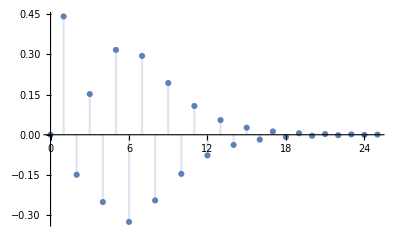

```mathematica
DiscretePlot[Subscript[x, l][k][[1]],{k,0,25},PlotRange->All]
```

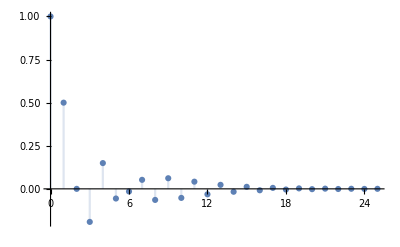

```mathematica
DiscretePlot[Subscript[x, l][k][[2]],{k,0,25},PlotRange->All]
```

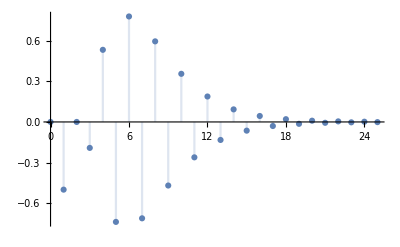

```mathematica
DiscretePlot[Subscript[x, l][k][[3]],{k,0,25},PlotRange->All]
```

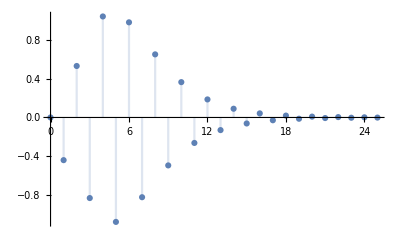

```mathematica
DiscretePlot[Subscript[x, l][k][[4]],{k,0,25},PlotRange->All]
```

```mathematica
lim_(k->∞) Subscript[x, l][k]
```

{{0},{0},{0},{0}}

```mathematica
(* La risposta libera, difatto, converge a zero perchè presenta modi naturali che sono successioni potenza, avente tutti base inferiore ad 1 in valore assoluto. *)
```

```mathematica
(* Passando allo studio della risposta libera in cui "azzero" alcuni stati ed altri no, bisogna scegliere in maniera adeguata il vettore dello stato iniziale; riprendo la matrice di cambiamento di base e la potenza k-esima della forma canonica di Jordan: *)
```

```mathematica
T =({{-37/85, -5/9, -8/9, -71/81}, {-18/85, -4/9, -16/9, -100/81}, {18/17, 4/3, 16/9, 50/27}, {1, 1, 0, 1}})
```

{{-37/85,-5/9,-8/9,-71/81},{-18/85,-4/9,-16/9,-100/81},{18/17,4/3,16/9,50/27},{1,1,0,1}}

```mathematica
({{(-2/3)^k, 0, 0, 0}, {0, (-1/2)^k, (-1)^(1+k) 2^(1-k) k, 0}, {0, 0, (-1/2)^k, 0}, {0, 0, 0, (-1/5)^k}})
```

{{(-2/3)^k,0,0,0},{0,(-1/2)^k,(-1)^(1+k) 2^(1-k) k,0},{0,0,(-1/2)^k,0},{0,0,0,(-1/5)^k}}

```mathematica
(* Ad esempio volendo azzerare nella risposta libera il modo (-1)^(1+k) 2^(1-k) k, è sufficiente prendere lo stato iniziale come combinazione lineare della prima, della seconda e della quarta colonna della matrice di cambiamento di base T, non considerando la terza colonna perchè è quella che contiene il modo naturale che non voglio considerare: *)
```

```mathematica
Subscript[x, 0] = T[[All,1]]+T[[All,2]]+T[[All,4]]
```

{-12857/6885,-13018/6885,1948/459,3}

```mathematica
Subscript[x, l][k_]:=Expand[FullSimplify[MatrixPower[A,k].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(-37/85 (-2/3)^k-5/9 (-1/2)^k-71/81 (-1/5)^k
-1/9 2^(2-k) ⅇ^(ⅈ k π)-1/85 2^(1+k) 3^(2-k) ⅇ^(ⅈ k π)-4/81 5^(2-k) ⅇ^(ⅈ k π)
1/3 2^(2-k) ⅇ^(ⅈ k π)+1/17 2^(1+k) 3^(2-k) ⅇ^(ⅈ k π)+2/27 5^(2-k) ⅇ^(ⅈ k π)
(-2/3)^k+(-1/2)^k+(-1/5)^k)

```mathematica
(* sempre al netto delle semplificazioni adottate da Mathematica, non risulta essere presente il modo polinomial-potenza considerato, inoltre compare  ⅇ^(ⅈ k π) = (-1)^k *)
```

```mathematica
(* Volendo invece "azzerare" nella risposta libera il modo naturale (-2/3)^k, prendo come stato iniziale una combinazione lineare della seconda della terza e della quarta colonna della matrice T, non considerando la prima colonna: *)
```

```mathematica
Subscript[x, 0] = T[[All,2]]+T[[All,3]]+T[[All,4]]
```

{-188/81,-280/81,134/27,2}

```mathematica
Subscript[x, l][k_]:=Expand[FullSimplify[MatrixPower[A,k].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(-13/9 2^-k ⅇ^(ⅈ k π)-71/81 5^-k ⅇ^(ⅈ k π)+5/9 2^(1-k) ⅇ^(ⅈ k π) k
-5/9 2^(2-k) ⅇ^(ⅈ k π)-4/81 5^(2-k) ⅇ^(ⅈ k π)+1/9 2^(3-k) ⅇ^(ⅈ k π) k
7/9 2^(2-k) ⅇ^(ⅈ k π)+2/27 5^(2-k) ⅇ^(ⅈ k π)-1/3 2^(3-k) ⅇ^(ⅈ k π) k
(-1/2)^k+(-1/5)^k+(-1)^(1+k) 2^(1-k) k)

```mathematica
(* Volendo attivare nella risposta libera solo il modo naturale (-2/3)^k, è come se volessi "azzerare" tutti gli altri modi, quindi prendo come stato iniziale una combinazione linera della prima colonna: *)
```

```mathematica
Subscript[x, 0] = T[[All,1]]
```

{-37/85,-18/85,18/17,1}

```mathematica
Subscript[x, l][k_]:=Expand[FullSimplify[MatrixPower[A,k].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(-37/85 (-2/3)^k
-1/85 2^(1+k) 3^(2-k) ⅇ^(ⅈ k π)
1/17 2^(1+k) 3^(2-k) ⅇ^(ⅈ k π)
(-2/3)^k)

```mathematica
(* Volendo attivare solo (-1/2)^k nella risposta libera, prendo come stato iniziale un vettore che è combinazione lineare della seconda colonna: *)
```

```mathematica
Subscript[x, 0] = T[[All,2]]
```

{-5/9,-4/9,4/3,1}

```mathematica
Subscript[x, l][k_]:=Expand[FullSimplify[MatrixPower[A,k].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(-5/9 (-1/2)^k
-1/9 (-1)^k 2^(2-k)
1/3 2^(2-k) ⅇ^(ⅈ k π)
(-1/2)^k)

```mathematica
(* Provando ad attivare solo il modo naturale (-1/5)^k nel calcolo della risposta libera: *)
```

```mathematica
Subscript[x, 0] = T[[All,4]]
```

{-71/81,-100/81,50/27,1}

```mathematica
Subscript[x, l][k_]:=Expand[FullSimplify[MatrixPower[A,k].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(-71/81 (-1/5)^k
-4/81 (-1)^k 5^(2-k)
2/27 (-1)^k 5^(2-k)
(-1/5)^k)

```mathematica
(* Invece per attivare il modo (-1)^(1+k) 2^(1-k) k, bisognerà attivare necessariamente il modo (-1/2)^k, in quanto si trovano entrambi sulla terza colonna : *)
```

```mathematica
Subscript[x, 0] = T[[All,3]]
```

{-8/9,-16/9,16/9,0}

```mathematica
Subscript[x, l][k_]:=Expand[FullSimplify[MatrixPower[A,k].Subscript[x, 0]]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(1/9 (-1)^(1+k) 2^(3-k)+5/9 (-1)^k 2^(1-k) k
-1/9 2^(4-k) ⅇ^(ⅈ k π)+1/9 2^(3-k) ⅇ^(ⅈ k π) k
1/9 2^(4-k) ⅇ^(ⅈ k π)-1/3 2^(3-k) ⅇ^(ⅈ k π) k
(-1)^(1+k) 2^(1-k) k)

```mathematica
(* Infatti notiamo che alcune componenti del vettore sono somma di due componenti, una data dal modo naturale (-1/2)^k, l'altra dal modo (-1)^(1+k) 2^(1-k) k. *)
```

```mathematica
(* Passo adesso all'analisi della funzione di trasferimento di questo sistema LTI-TD, definita anche in questo caso come un rapporto tra tue polinomi e facilmente ottenibile dalla formula: 
G(z) = C(zI-A)^-1 B+D *)
```

```mathematica
G[z_]:=Simplify[Cc.Inverse[z IdentityMatrix[4]-A].B + Dd]
```

```mathematica
G[z][[1,1]]
```

(60 (-1+3 z))/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
(* Per prima cosa analizzo gli zeri della funzione di trasferimento, che sono i valori per i quali si annulla il numeratore della F.D.T. : *)
```

```mathematica
Solve[Numerator[G[z]] == 0]
```

{{z→1/3}}

```mathematica
(* Poi nello studio del denominatore noto che grado del denominatore e numero di stati del sistema sono uguali, dunque il denominatore sarà uguale al polinomio caratteristico e i poli della funzione di trasferimento, che sono i valori per i quali si annulla il denominatore, saranno proprio gli autovalori del sistema; questo implica che quando ci si trova in questa condizione, per analizzare i modi naturali del sistema basterebbe studiare la funzione di trasferimento : *)
```

```mathematica
Solve[Denominator[G[z]] == 0]
```

{{z→-2/3},{z→-1/2},{z→-1/2},{z→-1/5}}

```mathematica
Factor[CharacteristicPolynomial[A,λ]]
```

1/60 (1+2 λ)^2 (2+3 λ) (1+5 λ)

```mathematica
(* Calcolo della risposta all'impulso del sistema: *)
```

```mathematica
(* La risposta all'impulso del sistema è definita come l'antitrasformata z della funzione di trasferimento: 
g(t) = ζ^-1[G[z]]; volendo verificarla passaggio per passaggio possiamo scomporre in maniera simbolica in fratti semplici, coerente secondo la Z-trasformata, la funzione di trasferimento e calcolarne i veri coefficienti con la formula generalizzata di Heaviside: *)
```

```mathematica
Expand[z Apart[G[z]/z]]
```

{{-30-(400 z)/(1+2 z)^2+(1120 z)/(3 (1+2 z))-(7290 z)/(7 (2+3 z))+(20000 z)/(21 (1+5 z))}}

```mathematica
{{-30-(400 z)/(1+2 z)^2+(1120 z)/(3 (1+2 z))-(7290 z)/(7 (2+3 z))+(20000 z)/(21 (1+5 z))}}
```

```mathematica
(* Subscript[C, 0]+Subscript[C, 22](z/(1/2+z)^2)+Subscript[C, 21](z/(1/2+z))+Subscript[C, 1](z/(2/3+z))+Subscript[C, 3](z/(1/5+z)) *)
```

```mathematica
Subscript[C, 1]= lim_(z->-2/3) (2/3+z)(G[z]/z)[[1,1]]
```

-2430/7

```mathematica
Subscript[C, 3] = lim_(z->-1/5) (1/5+z)(G[z]/z)[[1,1]]
```

4000/21

```mathematica
Subscript[C, 22]= lim_(z->-1/2) (1/2+z)^2(G[z]/z)[[1,1]]
```

-100

```mathematica
Subscript[C, 21]= 1/(1!)lim_(z->-1/2) D[((1/2+z)^2(G[z]/z))[[1,1]], z]
```

560/3

```mathematica
(* Per ottenere il termine Subscript[C, 0], tengo conto che sia legato al monomio z: )
```

```mathematica
Subscript[C, 0] = lim_(z->0) z(G[z]/z)[[1,1]]
```

-30

```mathematica
(* Scrivo adesso la risposta all'impulso : 
  g(k) = -30 δ(k)-400k(-1/2)^(k-1)1(k)+2240/3(-1/2)^k 1(k)-7290/7(-2/3)^k+4000/21(-1/5)^k, dove il termine costante genera un termine impulsivo, che non è un modo naturale del sistema, e che si valuta solo per k = 0 e per k > 0 non verrà più considerato. *)
```

```mathematica
g[k_]:= Subscript[C, 0] DiscreteDelta[k]+Subscript[C, 1](-2/3)^k UnitStep[k]+Subscript[C, 21](-1/2)^k UnitStep[k]+Subscript[C, 22] k(-1/2)^(k-1)UnitStep[k]+ Subscript[C, 3](-1/5)^k UnitStep[k]
```

```mathematica
g[k]
```

-30 DiscreteDelta[k]+35/3 (-1)^k 2^(4-k) UnitStep[k]-5/7 (-1)^k 2^(1+k) 3^(5-k) UnitStep[k]+32/21 (-1)^k 5^(3-k) UnitStep[k]-25 (-1)^(-1+k) 2^(3-k) k UnitStep[k]

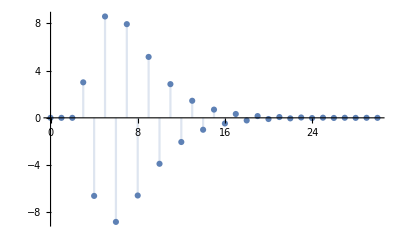

```mathematica
DiscretePlot[g[k],{k,0,30},PlotRange->All]
```

```mathematica
(* Studiando il grafico si nota come nei primi 3 istanti di tempo la risposta all'impulso valga 0, questo è dovuto alla differenza tra poli (4) e zeri (1) della funzione di trasferimento (4-1 = 3). Notiamo poi che la risposta all'impulso convergerà a zero, che possiamo dimostrare applicando il teorema del valore finale,essendo rispettate le condizioni, alla risposta all'impulso: *)
```

```mathematica
lim_(k->∞) g[k]
```

0

```mathematica
lim_(z->1) (1-z^-1)G[z][[1,1]]
```

0

```mathematica
(* Posso anche verificare, usando Mathematica con la funzione che calcola l' antiZ-trasformata della funzione di trasferimento, se i due grafici della risposta all'impulso combaciano: *)
```

```mathematica
g[k_]:=Expand[InverseZTransform[G[z],z,k]]
```

```mathematica
DiscretePlot[g[k][[1,1]],{k,0,30},PlotRange->All]
```

-Graphics-

```mathematica
(* Passo adesso al calcolo della risposta al gradino definita come Subscript[Y, f][z] = G[z] U[z], dove U[z] è la z-trasformata del gradino nel dominio z: *)
```

```mathematica
G[z][[1,1]]
```

(60 (-1+3 z))/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
U[z_] := ZTransform[1,k,z]
```

```mathematica
U[z]
```

z/(-1+z)

```mathematica
Subscript[Y, f][z] = G[z][[1,1]] U[z]
```

(60 z (-1+3 z))/((-1+z) (1+2 z)^2 (2+13 z+15 z^2))

```mathematica
(* Scompongo in maniera simbolica in fratti semplici, usando la funzione Apart: *)
```

```mathematica
Expand[z Apart[(Subscript[Y, f][z])/z]]
```

(4 z)/(9 (-1+z))-(400 z)/(3 (1+2 z)^2)+(640 z)/(3 (1+2 z))-(2916 z)/(7 (2+3 z))+(10000 z)/(63 (1+5 z))

```mathematica
(* In maniera simbolica: Subscript[D, 1](z/(z-1))+Subscript[D, 22](z/(z+1/2)^2)+Subscript[D, 21](z/(z+1/2))+Subscript[D, 3](z/(z+2/3))+Subscript[D, 4](z/(z+1/5)) , calcolo adesso i vari coefficienti Subscript[D, ij] utilizzando la formula di Heaviside, generalizzata per i poli multipli: *)
```

```mathematica
Subscript[D, 1] = lim_(z->1) (z-1)((Subscript[Y, f][z])/z)
```

4/9

```mathematica
Subscript[D, 3] = lim_(z->-2/3) ((z+2/3)((Subscript[Y, f][z])/z))
```

-972/7

```mathematica
Subscript[D, 4] = lim_(z->-1/5) ((z+1/5)((Subscript[Y, f][z])/z))
```

2000/63

```mathematica
Subscript[D, 22] = lim_(z->-1/2) ((z+1/2)^2((Subscript[Y, f][z])/z))
```

-100/3

```mathematica
Subscript[D, 21] = 1/(1!)lim_(z->-1/2) D[((z+1/2)^2((Subscript[Y, f][z])/z)), z]
```

320/3

```mathematica
(* Posso dunque riscrivere la risposta al gradino nel dominio del tempo, effettuando tutte le antiZ-trasformate necessarie: *)
```

```mathematica
Subscript[y, f][k_] := Subscript[D, 1] UnitStep[k]+ Subscript[D, 22] Binomial[k,1](-1/2)^(k-1)UnitStep[k]+ Subscript[D, 21](-1/2)^k UnitStep[k]+ Subscript[D, 3] (-2/3)^k UnitStep[k]+ Subscript[D, 4] (-1/5)^k UnitStep[k]
```

```mathematica
Subscript[y, f][k]
```

(4 UnitStep[k])/9+5/3 (-1)^k 2^(6-k) UnitStep[k]-1/7 (-1)^k 2^(2+k) 3^(5-k) UnitStep[k]+16/63 (-1)^k 5^(3-k) UnitStep[k]-25/3 (-1)^(-1+k) 2^(3-k) k UnitStep[k]

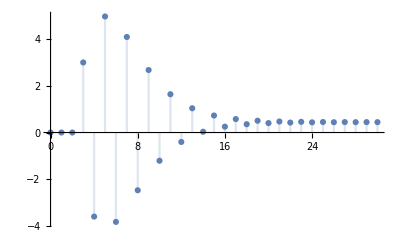

```mathematica
DiscretePlot[Subscript[y, f][k],{k,0,30},PlotRange->All]
```

```mathematica
(* Una volta rappresentata graficamente la risposta al gradino, la rappresento graficamente sovrapponendola al suo valore di regime, primo addendo della risposta al gradino, pari a 4/9: *)
```

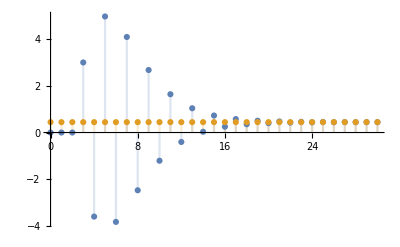

```mathematica
DiscretePlot[{Subscript[y, f][k],Subscript[D, 1]},{k,0,30},PlotRange->All]
```

```mathematica
(* Volendo verificare la correttezza del grafico e dunque della risposta al gradino sfruttando Mathematica, definisco la risposta al gradino con la sua formula Subscript[Y, f][z] = G[z](z/(z-1)) e ne calcolo la antiZ-trasformata: *)
```

```mathematica
Subscript[y, f][k_] := InverseZTransform[Subscript[Y, f][z],z,k]
```

```mathematica
DiscretePlot[{Subscript[y, f][k],4/9},{k,0,30},PlotRange->All]
```

-Graphics-

```mathematica
(* Passo adesso allo studio della risposta alla rampa, definisco un ingresso u(k) = k, una semplice retta e definisco la risposta alla rampa come Subscript[y, f](z) = G[z]U[z], dove G[z] è la funzione di trasferimento ed U[z] è la z-trasformata del mio ingresso u(k): *)
```

```mathematica
u[k_] := k
```

```mathematica
U[z] = ZTransform[u[k],k,z]
```

z/(-1+z)^2

```mathematica
Subscript[y, f][z_] := G[z][[1,1]]U[z]
```

```mathematica
Subscript[y, f][z]
```

(60 z (-1+3 z))/((-1+z)^2 (1+2 z)^2 (2+13 z+15 z^2))

```mathematica
Subscript[y, rampa][k_] := Simplify[InverseZTransform[Subscript[y, f][z],z,k]]
```

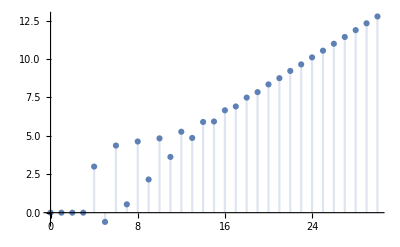

```mathematica
DiscretePlot[Subscript[y, rampa][k],{k,0,30},PlotRange->All]
```

```mathematica
(* Verifico il calcolo della risposta alla rampa calcolando i vari coefficienti tramite la formula di Heaviside, partendo dalla scomposizione in fratti semplici: *)
```

```mathematica
Expand[z Apart[(Subscript[y, f][z])/z]]
```

(4 z)/(9 (-1+z)^2)-(76 z)/(135 (-1+z))+(800 z)/(9 (1+2 z)^2)-(3040 z)/(27 (1+2 z))+(8748 z)/(35 (2+3 z))-(25000 z)/(189 (1+5 z))

```mathematica
(* Subscript[D, 12](z/(z-1)^2)+ Subscript[D, 11](z/(z-1)) +Subscript[D, 22](z/(z+1/2)^2)+Subscript[D, 21](z/(z+1/2))+Subscript[D, 3](z/(z+2/3))+Subscript[D, 4](z/(z+1/5)) *)
```

```mathematica
Subscript[D, 12] = lim_(z->1) (z-1)^2((Subscript[y, f][z])/z)
```

4/9

```mathematica
Subscript[D, 11] = lim_(z->1) D[((z-1)^2((Subscript[y, f][z])/z)), z]
```

-76/135

```mathematica
Subscript[D, 22] = lim_(z->-1/2) ((z+1/2)^2((Subscript[y, f][z])/z))
```

200/9

```mathematica
Subscript[D, 21] = (1/1!)lim_(z->-1/2) D[((z+1/2)^2(Subscript[y, f][z]/z)), z]
```

-1520/27

```mathematica
Subscript[D, 3] = lim_(z->-2/3) ((z+2/3)((Subscript[y, f][z])/z))
```

2916/35

```mathematica
Subscript[D, 4] = lim_(z->-1/5) ((z+1/5)((Subscript[y, f][z])/z))
```

-5000/189

```mathematica
(* Scrivo adesso la risposta alla rampa, eseguendo le antiZ-trasformate: *)
```

```mathematica
Subscript[y, rampa][k_] := Subscript[D, 12] k UnitStep[k]+Subscript[D, 11] UnitStep[k]+Subscript[D, 22] k(-1/2)^(k-1)UnitStep[k]+ Subscript[D, 21] (-1/2)^k UnitStep[k]+ Subscript[D, 3](-2/3)^k UnitStep[k]+ Subscript[D, 4](-1/5)^k UnitStep[k]
```

```mathematica
DiscretePlot[Subscript[y, rampa][k],{k,0,30},PlotRange->All]
```

-Graphics-

```mathematica
(* Difatto calcolando il limite per k che tende ad infinito della risposta alla rampa : *)
```

```mathematica
lim_(k->∞) Subscript[y, rampa][k]
```

∞

```mathematica
(* Costruisco una rappresentazione I/U nel dominio del tempo, partendo dalla funzione di trasferimento: *)
```

```mathematica
G[z][[1,1]]
```

(60 (-1+3 z))/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
(* Definendo Subscript[y, f](z)=G(z)u(z), riscrivo la funzione di trasferimento come 
G(z)=(Subscript[y, f](z))/(u(z)) e moltiplico ambo i membri per la quantità u(z) e per il denominatore della funzione di trasferimento, ottenendo: 60(-1+3 z)(u(z)) = Subscript[y, f](z)(1+2 z)^2 (2+13 z+15 z^2); eseguendo i calcoli:
  -60u(z)+180z(u(z)) = 60 z^4 Subscript[y, f](z)+112 z^3 Subscript[y, f](z)+75 z^2 Subscript[y, f](z)+21z Subscript[y, f](z)+2 Subscript[y, f](z) ,diventa una identità algebrica in z ed applicando il teorema dello shifting sinistro (anticipo) di ordine n sulla Z-trasformata ottengo una identità differenziale: 
60y(k+4)+112y(k+3)+75y(k+2)+21y(k+1)+2y(k) = 180u(k+1)-60u(k), questa sarà la rappresentazione I/U del sistema dinamico, provo adesso a calcolare la risposta libera partendo dallo stato iniziale Subscript[x, 0]: *)
```

```mathematica
Subscript[x, 0]=({{0}, {1}, {0}, {0}})
```

{{0},{1},{0},{0}}

```mathematica
(* Imposto l'equazione alle differenze: *)
```

```mathematica
Eqdiff = 60y[k+4]+112y[k+3]+75y[k+2]+21y[k+1]+2y[k] == 180U[k+1]-60U[k]
```

2 y[k]+21 y[1+k]+75 y[2+k]+112 y[3+k]+60 y[4+k]==-60 U[k]+180 U[1+k]

```mathematica
(* La trasformo nel dominio z: *)
```

```mathematica
ZTransform[Eqdiff,k,z]
```

2 ZTransform[y[k],k,z]+21 (-z y[0]+z ZTransform[y[k],k,z])+75 (-z^2 y[0]-z y[1]+z^2 ZTransform[y[k],k,z])+112 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 ZTransform[y[k],k,z])+60 (-z^4 y[0]-z^3 y[1]-z^2 y[2]-z y[3]+z^4 ZTransform[y[k],k,z])==-60 ZTransform[U[k],k,z]+180 (-z U[0]+z ZTransform[U[k],k,z])

```mathematica
(* Sostituisco i simboli Y(z) e Subscript[U, 1][z] agli oggetti Ztransform ed azzero la quantità u(0): *)
```

```mathematica
%/.{ZTransform[y[k],k,z]->Y[z],ZTransform[U[k],k,z]->Subscript[U, 1][z]}
```

2 Y[z]+21 (-z y[0]+z Y[z])+75 (-z^2 y[0]-z y[1]+z^2 Y[z])+112 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])+60 (-z^4 y[0]-z^3 y[1]-z^2 y[2]-z y[3]+z^4 Y[z])==-60 U_1[z]+180 (-z U[0]+z U_1[z])

```mathematica
Eqdifferenz=%/.{U[0]->0}
```

2 Y[z]+21 (-z y[0]+z Y[z])+75 (-z^2 y[0]-z y[1]+z^2 Y[z])+112 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])+60 (-z^4 y[0]-z^3 y[1]-z^2 y[2]-z y[3]+z^4 Y[z])==-60 U_1[z]+180 z U_1[z]

```mathematica
(* Risolvo rispetto all'incognita Y[z] ed estraggo la risposta in z: *)
```

```mathematica
Solve[Eqdifferenz,Y[z]]
```

{{Y[z]→(21 z y[0]+75 z^2 y[0]+112 z^3 y[0]+60 z^4 y[0]+75 z y[1]+112 z^2 y[1]+60 z^3 y[1]+112 z y[2]+60 z^2 y[2]+60 z y[3]-60 U_1[z]+180 z U_1[z])/((1+2 z)^2 (2+13 z+15 z^2))}}

```mathematica
Rispostaz=Solve[Eqdifferenz,Y[z]][[1,1]][[2]]
```

(21 z y[0]+75 z^2 y[0]+112 z^3 y[0]+60 z^4 y[0]+75 z y[1]+112 z^2 y[1]+60 z^3 y[1]+112 z y[2]+60 z^2 y[2]+60 z y[3]-60 U_1[z]+180 z U_1[z])/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
(* Separo la componente forzata (secondo addendo) dalla risposta libera: *)
```

```mathematica
Collect[Rispostaz,Subscript[U, 1][z]]
```

(21 z y[0]+75 z^2 y[0]+112 z^3 y[0]+60 z^4 y[0]+75 z y[1]+112 z^2 y[1]+60 z^3 y[1]+112 z y[2]+60 z^2 y[2]+60 z y[3])/((1+2 z)^2 (2+13 z+15 z^2))+((-60+180 z) U_1[z])/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
Rispliberaz=%[[1]]
```

(21 z y[0]+75 z^2 y[0]+112 z^3 y[0]+60 z^4 y[0]+75 z y[1]+112 z^2 y[1]+60 z^3 y[1]+112 z y[2]+60 z^2 y[2]+60 z y[3])/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
(* Assegno le condizioni iniziali a partire dallo stato Subscript[x, 0] per risolvere l'equazione alle differenze: *)
```

```mathematica
y[0] = (Cc.Subscript[x, 0])[[1,1]]
```

-2

```mathematica
y[1]=(Cc.A.Subscript[x, 0])[[1,1]]
```

1

```mathematica
y[2]=(Cc.A.A.Subscript[x, 0])[[1,1]]
```

0

```mathematica
y[3]=(Cc.A.A.A.Subscript[x, 0])[[1,1]]
```

23/20

```mathematica
(* Dunque la risposta libera sarà : *)
```

```mathematica
Rispliberaz
```

(102 z-38 z^2-164 z^3-120 z^4)/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
(* Adesso verifico che la risposta libera sia una combinazione lineare di modi naturali del sistema: *)
```

```mathematica
Expand[z Apart[Rispliberaz/z]]
```

-(380 z)/(3 (1+2 z)^2)+(1304 z)/(9 (1+2 z))-(2430 z)/(7 (2+3 z))+(13000 z)/(63 (1+5 z))

```mathematica
(* La riscrivo in maniera simbolica in fratti semplici:
Subscript[D, 22](z/(z+1/2)^2)+Subscript[D, 21](z/(z+1/2))+Subscript[D, 1](z/(z+2/3))+ Subscript[D, 3](z/(z+1/5)) *)
```

```mathematica
Subscript[D, 1]= lim_(z->-2/3) (z+2/3)(Rispliberaz/z)
```

-810/7

```mathematica
Subscript[D, 3]= lim_(z->-1/5) (z+1/5)(Rispliberaz/z)
```

2600/63

```mathematica
Subscript[D, 22]= lim_(z->-1/2) (z+1/2)^2(Rispliberaz/z)
```

-95/3

```mathematica
Subscript[D, 21]= lim_(z->-1/2) D[((z+1/2)^2(Rispliberaz/z)), z]
```

652/9

```mathematica
(* Dunque posso adesso scrivere la risposta libera come una succesione di questo tipo: *)
```

```mathematica
rispLibera[k_] :=  Subscript[D, 22] Binomial[k,1](-1/2)^(k-1)UnitStep[k]+Subscript[D, 21](-1/2)^k UnitStep[k]+ Subscript[D, 1](-2/3)^k UnitStep[k]+ Subscript[D, 3](-1/5)^k UnitStep[k]
```

```mathematica
(* Che è ovviamente combinazione lineare dei modi naturali del sistema. *)
```

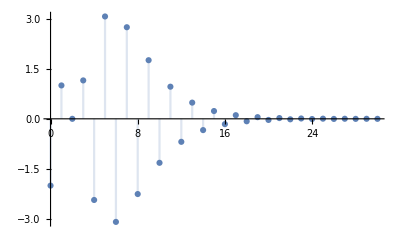

```mathematica
DiscretePlot[rispLibera[k],{k,0,30},PlotRange->All]
```

```mathematica
(* Per verificare la correttezza delle condizioni iniziali: *)
```

```mathematica
rispLibera[0]
```

-2

```mathematica
rispLibera[1]
```

1

```mathematica
rispLibera[2]
```

0

```mathematica
rispLibera[3]
```

23/20

```mathematica
(* Passo adesso al determinare la risposta del sistema all'ingresso u(k) = 1(-k); questo è un gradino di ampiezza unitaria, applicato nel passato remoto, dunque l'istante di applicazione di questo gradino Subscript[k, 0] è tale che Subscript[k, 0] -> ∞: *)
```

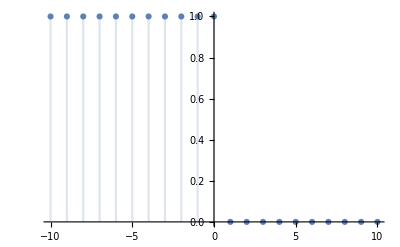

```mathematica
DiscretePlot[UnitStep[-k],{k,-10,10}]
```

```mathematica
(* All'istante k = 0, commuta e cambia valore a 0; dunque bisogna analizzare 2 casi, la risposta del sistema per k<0 e la risposta del sistema per k>=0. Dovrò dunque definire una funzione a tratti.
Scrivo la risposta al gradino unitario, applicato in corrispondenza di un istante Subscript[k, 0] diverso da 0: (Subscript[C, 1](-2/3)^(k-)+Subscript[C, 3](-1/5)^(k-)+Subscript[C, 22] k(-1/2)^(k-1-Subscript[k, 0])+ Subscript[C, 21](-1/2)^(k-Subscript[k, 0]))1(k-Subscript[k, 0])+Subscript[C, 4] 1(k-Subscript[k, 0]), riprendo i coefficienti Subscript[C, ij] dai calcoli della risposta al gradino svolti in precedenza. *)
```

```mathematica
Subscript[C, 1] = -972/7
```

-972/7

```mathematica
Subscript[C, 3] = 2000/63
```

2000/63

```mathematica
Subscript[C, 22] = -100/3
```

-100/3

```mathematica
Subscript[C, 21] = 320/3
```

320/3

```mathematica
Subscript[C, 4] = lim_(z->1) (z-1)(G[z][[1,1]] 1/(z-1))
```

4/9

```mathematica
G[z][[1,1]]
```

(60 (-1+3 z))/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
G[1][[1,1]]
```

4/9

```mathematica
(* Per k > 0, si ha assenza di ingresso, perchè commuta a zero, quindi bisogna valutare la risposta libera a partire da opportune condizioni iniziali, e saranno costanti e pari a G[1] = 4/9, perchè per k<0 l'uscita era costante e quindi le condizioni iniziali saranno costanti al valore dell'uscita per k<0 che è 4/9; dal modello I/U determinato in precedenza riprendo la mia risposta libera in z, avendo già adottato precedentemente tutte le semplificazioni del caso ed assegno le nuove condizioni iniziali: y(0)=y(1)=y(2)=y(3)= G(1)=4/9 : *)
```

```mathematica
Rispliberaz = (21 z y[0]+75 z^2 y[0]+112 z^3 y[0]+60 z^4 y[0]+75 z y[1]+112 z^2 y[1]+60 z^3 y[1]+112 z y[2]+60 z^2 y[2]+60 z y[3])/((1+2 z)^2 (2+13 z+15 z^2))
```

(21 z y[0]+75 z^2 y[0]+112 z^3 y[0]+60 z^4 y[0]+75 z y[1]+112 z^2 y[1]+60 z^3 y[1]+112 z y[2]+60 z^2 y[2]+60 z y[3])/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
y[0]= y[1] = y[2] = y[3] = 4/9
```

4/9

```mathematica
Rispliberaz
```

((1072 z)/9+(988 z^2)/9+(688 z^3)/9+(80 z^4)/3)/((1+2 z)^2 (2+13 z+15 z^2))

```mathematica
(* Riscrivo l'espansione in fratti semplici: *)
```

```mathematica
Expand[z Apart[Rispliberaz/z]]
```

-(320 z)/(3 (1+2 z)^2)+(320 z)/(3 (1+2 z))-(1944 z)/(7 (2+3 z))+(12500 z)/(63 (1+5 z))

```mathematica
(*Subscript[D, 22](z/(z+1/2)^2)+Subscript[D, 21](z/(z+1/2))+Subscript[D, 1](z/(z+2/3))+ Subscript[D, 3](z/(z+1/5)) riscrivendola in maniera simbolica, ricalcolo i coefficienti come in precedenza: *)
```

```mathematica
Subscript[D, 1]= lim_(z->-2/3) (z+2/3)(Rispliberaz/z)
```

-648/7

```mathematica
Subscript[D, 3]= lim_(z->-1/5) (z+1/5)(Rispliberaz/z)
```

2500/63

```mathematica
Subscript[D, 22]= lim_(z->-1/2) (z+1/2)^2(Rispliberaz/z)
```

-80/3

```mathematica
Subscript[D, 21]= lim_(z->-1/2) D[((z+1/2)^2(Rispliberaz/z)), z]
```

160/3

```mathematica
(* Dunque posso scrivere la risposta libera come una successione che dovrò poi shiftare di 3 campioni: *)
```

```mathematica
f[k_]:=Subscript[D, 1] (-2/3)^k+Subscript[D, 22] k(-1/2)^(k-1)+Subscript[D, 21] (-1/2)^k+Subscript[D, 3] (-1/5)^k
```

```mathematica
f[0]
```

4/9

```mathematica
f[1]
```

4/9

```mathematica
f[2]
```

4/9

```mathematica
f[3]
```

4/9

```mathematica
(* Per ottenere il risultato cercato, e dunque la risposta del sistema per k>0, dovrò shiftare di 3 unità di tempo verso sinistra la mia risposta libera, e sarà la seguente funzione a tratti: *)
```

```mathematica
Subscript[y, fin][k_]:=Piecewise[{{G[1][[1,1]], k<0}, {f[k+3], k>=0}}]
```

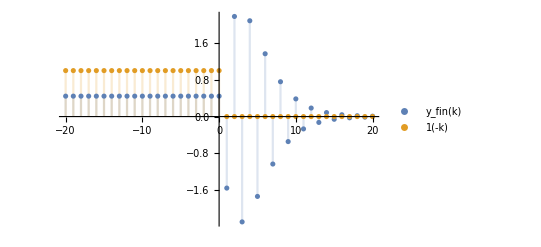

```mathematica
DiscretePlot[{Subscript[y, fin][k],UnitStep[-k]},{k,-20,20},PlotRange->All,PlotLegends->{"y_fin(k)","1(-k)"}]
```